```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poslavsky/Projects/redberry/bcbcnlo/src/check_Berezhnoy

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->TraditionalForm}];
PrependTo[$Path,ToFileName[ParentDirectory[NotebookDirectory[]],"pkg"]];
```

```mathematica
<<FeynArts`FeynArts`
$Verbose=False;
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
$ExcludeTopologies[V4onExt]=FreeQ[Cases[#,Propagator[External][__]],Vertex[4]]&;
```

```mathematica
top=CreateTopologies[1,1->4,Adjacencies->3,ExcludeTopologies->{WFCorrections,Tadpoles,V4onExt}];
```

```mathematica
tmp=InsertFields[top,{V[1]}->{Amp= Amp/.fm:DiracSpinor[qb,MB].(mx___/;FreeQ[{mx},DiracSpinor]). DiracSpinor[qc-p3,MB]:>$LineA1[Dot[mx]];
Amp=Amp/.fm:DiracSpinor[qc,MC].(mx___/;FreeQ[{mx},DiracSpinor]). DiracSpinor[qb-p4,MC]:>$LineA2[Dot[mx]];F[3,{2}],-F[3,{2}],F[4,{3}],-F[4,{3}]},Model->"SMQCD",ExcludeParticles->{V[1],V[2],V[3],V[4],S[_]},InsertionLevel->{Particles}];
```

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 1 Particles insertion

> Top. 9: 1 Particles insertion

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 2 Particles insertions

> Top. 13: 2 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 1 Particles insertion

> Top. 18: 1 Particles insertion

> Top. 19: 2 Particles insertions

> Top. 20: 2 Particles insertions

> Top. 21: 12 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 1 Particles insertion

> Top. 24: 1 Particles insertion

> Top. 25: 1 Particles insertion

> Top. 26: 1 Particles insertion

> Top. 27: 1 Particles insertion

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 2 Particles insertions

> Top. 33: 1 Particles insertion

> Top. 34: 1 Particles insertion

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 0 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

> Top. 43: 0 Particles insertions

> Top. 44: 0 Particles insertions

> Top. 45: 0 Particles insertions

> Top. 46: 0 Particles insertions

> Top. 47: 0 Particles insertions

> Top. 48: 0 Particles insertions

> Top. 49: 0 Particles insertions

> Top. 50: 0 Particles insertions

> Top. 51: 0 Particles insertions

> Top. 52: 0 Particles insertions

> Top. 53: 0 Particles insertions

> Top. 54: 2 Particles insertions

> Top. 55: 1 Particles insertion

> Top. 56: 1 Particles insertion

> Top. 57: 0 Particles insertions

> Top. 58: 0 Particles insertions

> Top. 59: 0 Particles insertions

> Top. 60: 0 Particles insertions

> Top. 61: 0 Particles insertions

> Top. 62: 0 Particles insertions

> Top. 63: 0 Particles insertions

> Top. 64: 0 Particles insertions

> Top. 65: 0 Particles insertions

> Top. 66: 0 Particles insertions

> Top. 67: 0 Particles insertions

> Top. 68: 0 Particles insertions

> Top. 69: 0 Particles insertions

> Top. 70: 0 Particles insertions

> Top. 71: 1 Particles insertion

> Top. 72: 1 Particles insertion

> Top. 73: 1 Particles insertion

> Top. 74: 1 Particles insertion

> Top. 75: 1 Particles insertion

> Top. 76: 1 Particles insertion

> Top. 77: 1 Particles insertion

> Top. 78: 0 Particles insertions

> Top. 79: 0 Particles insertions

> Top. 80: 0 Particles insertions

> Top. 81: 0 Particles insertions

> Top. 82: 0 Particles insertions

> Top. 83: 0 Particles insertions

> Top. 84: 0 Particles insertions

> Top. 85: 0 Particles insertions

> Top. 86: 1 Particles insertion

> Top. 87: 1 Particles insertion

> Top. 88: 0 Particles insertions

> Top. 89: 0 Particles insertions

> Top. 90: 0 Particles insertions

> Top. 91: 0 Particles insertions

> Top. 92: 8 Particles insertions

> Top. 93: 1 Particles insertion

> Top. 94: 0 Particles insertions

> Top. 95: 0 Particles insertions

> Top. 96: 0 Particles insertions

> Top. 97: 0 Particles insertions

> Top. 98: 8 Particles insertions

> Top. 99: 1 Particles insertion

> Top. 100: 8 Particles insertions

> Top. 101: 1 Particles insertion

> Top. 102: 8 Particles insertions

> Top. 103: 1 Particles insertion

> Top. 104: 0 Particles insertions

> Top. 105: 0 Particles insertions

> Top. 106: 0 Particles insertions

> Top. 107: 0 Particles insertions

> Top. 108: 0 Particles insertions

> Top. 109: 0 Particles insertions

> Top. 110: 0 Particles insertions

> Top. 111: 0 Particles insertions

> Top. 112: 0 Particles insertions

> Top. 113: 0 Particles insertions

> Top. 114: 0 Particles insertions

> Top. 115: 0 Particles insertions

> Top. 116: 0 Particles insertions

> Top. 117: 0 Particles insertions

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 86 Particles insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

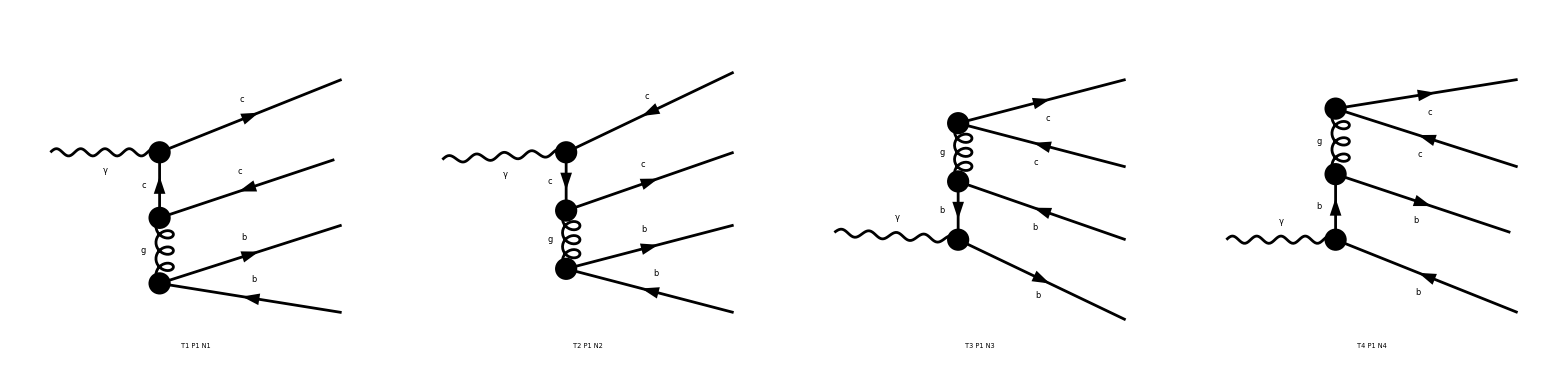

```mathematica
Paint[tmp,ColumnsXRows->{4,1}];
```

```mathematica
FactorSUNT[exp_DiracTrace]:=Module[{temp=List@@exp,reversed},
temp=(Collect[#,_SUNT])&/@temp;
temp=Cases[temp,_SUNT,Infinity];
reversed=FreeQ[temp,{___,SUNT[_,_,ci_],SUNT[_,ci_,_],___}];
temp=temp/.{SUNT[c_,_,_]:>SUNT[c]};
If[reversed,temp=Reverse[temp]];
temp=SUNTrace[Dot@@temp] (exp/.SUNT[_,_,_]->1);
Return[temp];
];
```

```mathematica
FAToFC[d__]:=Module[{temp},
temp=CreateFeynAmp[d,PreFactor->1]/.{FourMomentum[Incoming,1]->p3+p4,
FourMomentum[Outgoing,1]->qc,
FourMomentum[Outgoing,2]->p4-qb,
FourMomentum[Outgoing,3]->qb,
FourMomentum[Outgoing,4]-> p3-qc,
EL->e,GS->Gstrong};
temp=(Part[#,2]&)/@(List@@ToFA1Conventions[temp]);
temp=temp/.{DiracMatrix[li_].ChiralityProjector[1]:>DiracMatrix[li]/2,DiracMatrix[li_].ChiralityProjector[-1]:>DiracMatrix[li]/2};
temp=temp/.{exp_DiracTrace:>FactorSUNT[exp]};
temp=temp/.{IndexDelta[Index[x1_,y1_],Index[x2_,y2_]]:>1,SUNT[c_,_,_]:>SUNT[c],SumOver[__]->1,PolarizationVector[___]->1};
Return[temp];
];
```

```mathematica
Amp= FAToFC[tmp];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

> Top. 5: 2 Particles amplitudes

> Top. 6: 2 Particles amplitudes

> Top. 7: 1 Particles amplitude

> Top. 8: 1 Particles amplitude

> Top. 9: 2 Particles amplitudes

> Top. 10: 2 Particles amplitudes

> Top. 11: 12 Particles amplitudes

> Top. 12: 1 Particles amplitude

> Top. 13: 1 Particles amplitude

> Top. 14: 1 Particles amplitude

> Top. 15: 1 Particles amplitude

> Top. 16: 1 Particles amplitude

> Top. 17: 2 Particles amplitudes

> Top. 18: 1 Particles amplitude

> Top. 19: 1 Particles amplitude

> Top. 20: 2 Particles amplitudes

> Top. 21: 1 Particles amplitude

> Top. 22: 1 Particles amplitude

> Top. 23: 1 Particles amplitude

> Top. 24: 1 Particles amplitude

> Top. 25: 1 Particles amplitude

> Top. 26: 1 Particles amplitude

> Top. 27: 1 Particles amplitude

> Top. 28: 1 Particles amplitude

> Top. 29: 1 Particles amplitude

> Top. 30: 1 Particles amplitude

> Top. 31: 1 Particles amplitude

> Top. 32: 8 Particles amplitudes

> Top. 33: 1 Particles amplitude

> Top. 34: 8 Particles amplitudes

> Top. 35: 1 Particles amplitude

> Top. 36: 8 Particles amplitudes

> Top. 37: 1 Particles amplitude

> Top. 38: 8 Particles amplitudes

> Top. 39: 1 Particles amplitude

in total: 86 Particles amplitudes

```mathematica
Amp
```

{1/(p3+qb-qc)^2 g(li2,li3) 1/((p3+p4-qc)^2-MC^2) DiracSpinor(qb,MB).(-ⅈ Gstrong ga(li3) SUNT(Glu6)).DiracSpinor(qc-p3,MB) DiracSpinor(qc,MC).(-2/3 ⅈ e ga(li1)).(gs(-p3-p4+qc)+MC).(-ⅈ Gstrong ga(li2) SUNT(Glu6)).DiracSpinor(qb-p4,MC),1/((-p3-qb)^2-MC^2) 1/(p3+qb-qc)^2 g(li2,li3) DiracSpinor(qb,MB).(-ⅈ Gstrong ga(li3) SUNT(Glu6)).DiracSpinor(qc-p3,MB) DiracSpinor(qc,MC).(-ⅈ Gstrong ga(li2) SUNT(Glu6)).(gs(p3+qb)+MC).(-2/3 ⅈ e ga(li1)).DiracSpinor(qb-p4,MC),1/(-p4+qb-qc)^2 g(li2,li3) 1/((p3+p4-qb)^2-MB^2) DiracSpinor(qc,MC).(-ⅈ Gstrong ga(li2) SUNT(Glu6)).DiracSpinor(qb-p4,MC) DiracSpinor(qb,MB).(1/3 ⅈ e ga(li1)).(gs(-p3-p4+qb)+MB).(-ⅈ Gstrong ga(li3) SUNT(Glu6)).DiracSpinor(qc-p3,MB),1/((-p4-qc)^2-MB^2) 1/(-p4+qb-qc)^2 g(li2,li3) DiracSpinor(qc,MC).(-ⅈ Gstrong ga(li2) SUNT(Glu6)).DiracSpinor(qb-p4,MC) DiracSpinor(qb,MB).(-ⅈ Gstrong ga(li3) SUNT(Glu6)).(gs(p4+qc)+MB).(1/3 ⅈ e ga(li1)).DiracSpinor(qc-p3,MB)}

```mathematica
Amp= Amp/.fm:DiracSpinor[qb,MB].(mx___/;FreeQ[{mx},DiracSpinor]). DiracSpinor[qc-p3,MB]:>$LineA1[Dot[mx]];
Amp=Amp/.fm:DiracSpinor[qc,MC].(mx___/;FreeQ[{mx},DiracSpinor]). DiracSpinor[qb-p4,MC]:>$LineA2[Dot[mx]];
```

```mathematica
Amp
```

{1/(p3+qb-qc)^2 g(li2,li3) 1/((p3+p4-qc)^2-MC^2) $LineA1(-ⅈ Gstrong ga(li3) SUNT(Glu6)) $LineA2((-2/3 ⅈ e ga(li1)).(gs(-p3-p4+qc)+MC).(-ⅈ Gstrong ga(li2) SUNT(Glu6))),1/((-p3-qb)^2-MC^2) 1/(p3+qb-qc)^2 g(li2,li3) $LineA1(-ⅈ Gstrong ga(li3) SUNT(Glu6)) $LineA2((-ⅈ Gstrong ga(li2) SUNT(Glu6)).(gs(p3+qb)+MC).(-2/3 ⅈ e ga(li1))),1/(-p4+qb-qc)^2 g(li2,li3) 1/((p3+p4-qb)^2-MB^2) $LineA2(-ⅈ Gstrong ga(li2) SUNT(Glu6)) $LineA1((1/3 ⅈ e ga(li1)).(gs(-p3-p4+qb)+MB).(-ⅈ Gstrong ga(li3) SUNT(Glu6))),1/((-p4-qc)^2-MB^2) 1/(-p4+qb-qc)^2 g(li2,li3) $LineA2(-ⅈ Gstrong ga(li2) SUNT(Glu6)) $LineA1((-ⅈ Gstrong ga(li3) SUNT(Glu6)).(gs(p4+qc)+MB).(1/3 ⅈ e ga(li1)))}

```mathematica
(*SetDirectory[ToFileName[NotebookDirectory[], "dmp"]];*)
Export["Amp.m", Amp];
ResetDirectory[];
```